```mathematica
a1=Import["G:\\calc-online\\gpd\\formfactor\\lowestorder\\result\\EMformfactor-dbar-ubar-L1.wdx"];
F1all=Query[1]@a1;
F2all=Query[2]@a1;
F1fall=Interpolation[F1all];
F2fall=Interpolation[F2all];
a2=Import["G:\\calc-online\\gpd\\formfactor\\lowestorder\\result\\EMformfactor-dbar-ubar-L1-meson.wdx"];
F1me=Query[1]@a2;
F2me=Query[2]@a2;
F1fme=Interpolation[F1me];
F2fme=Interpolation[F2me];
```

```mathematica
a3=Import["G:\\calc-online\\gpd\\formfactor\\lowestorder\\result\\EMformfactor-dbar-ubar-L1-polarize.wdx"];
F1po=Query[1]@a3;
F2po=Query[2]@a3;
F1fpo=Interpolation[F1po];
F2fpo=Interpolation[F2po];
```

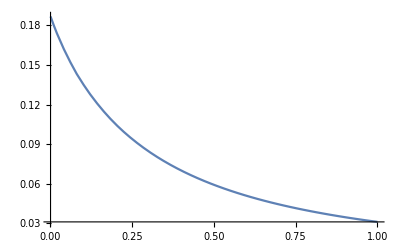

```mathematica
Plot[F1fall[-t],{t,0.001,1}]
```

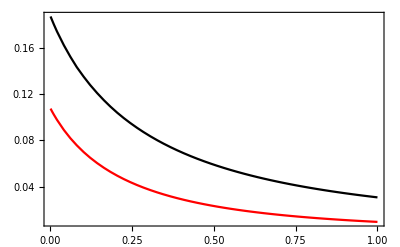
-Graphics-F_1^(d̄-ū)t

```mathematica
F1p=Labeled[Show[Plot[F1fall[-t],{t,0.001,1},PlotRange->All,PlotStyle->{Black,Thick}],Plot[F1fme[-t],{t,0.001,1},PlotRange->All,PlotStyle->{Red,Thick}],AxesStyle->Directive[16],Frame->True,FrameStyle->Directive[Thick,20]],
{SubsuperscriptBox[F,1,OverscriptBox[d,_]-OverscriptBox[u,_]]//DisplayForm,
StyleBox["t",FontSlant->"Italic"]//DisplayForm},{Left,Bottom,Right},LabelStyle->20]
```

```mathematica
StyleBox[SubscriptBox[F,1],FontSlant->"Italic"]//DisplayForm
```

```mathematica
SubsuperscriptBox[F,1,OverscriptBox[d,_]-OverscriptBox[u,_]]//DisplayForm
```

F_1^(d̄-ū)

```mathematica
OverscriptBox[u,_]//DisplayForm
```

ū

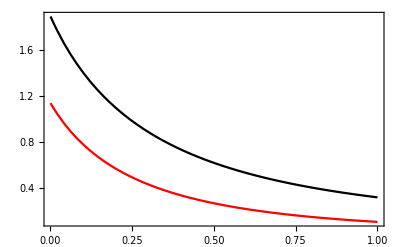
-Graphics-F_2^(d̄-ū)t

```mathematica
F2p=Labeled[Show[Plot[F2fall[-t],{t,0.001,1},PlotRange->All,PlotStyle->{Black,Thick}],Plot[F2fme[-t],{t,0.001,1},PlotRange->All,PlotStyle->{Red,Thick}],AxesStyle->Directive[16],Frame->True,FrameStyle->Directive[Thick,20]],
{SubsuperscriptBox[F,2,OverscriptBox[d,_]-OverscriptBox[u,_]]//DisplayForm,
StyleBox["t",FontSlant->"Italic"]//DisplayForm},{Left,Bottom,Right},LabelStyle->20]
```

```mathematica
path1=FileNameJoin[{"G:\\calc-online\\gpd\\formfactor\\lowestorder\\result",
"F1-823.pdf"}];
Export[path1,F1p]

path2=FileNameJoin[{"G:\\calc-online\\gpd\\formfactor\\lowestorder\\result",
"F2-823.pdf"}];
Export[path2,F2p]
```

G:\calc-online\gpd\formfactor\lowestorder\result\F1-823.pdf

G:\calc-online\gpd\formfactor\lowestorder\result\F2-823.pdf

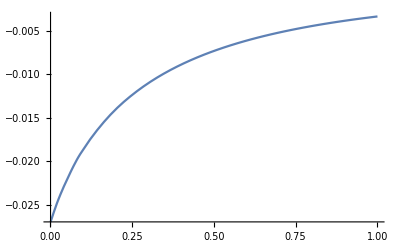

```mathematica
Plot[F1fpo[-t],{t,0.001,1}]
```

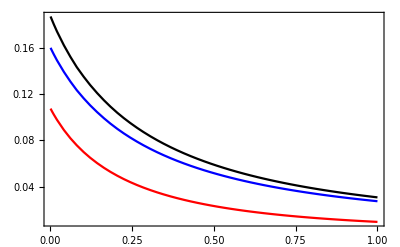
-Graphics-F_1^(d̄-ū)t

```mathematica
F1pn=Labeled[Show[Plot[F1fall[-t],{t,0.001,1},PlotRange->All,PlotStyle->{Black,Thick}],Plot[F1fme[-t],{t,0.001,1},PlotRange->All,PlotStyle->{Red,Thick}],Plot[F1fall[-t]+F1fpo[-t],{t,0.001,1},PlotRange->All,PlotStyle->{Blue,Thick}],AxesStyle->Directive[16],Frame->True,FrameStyle->Directive[Thick,20]],
{SubsuperscriptBox[F,1,OverscriptBox[d,_]-OverscriptBox[u,_]]//DisplayForm,
StyleBox["t",FontSlant->"Italic"]//DisplayForm},{Left,Bottom,Right},LabelStyle->20]
```

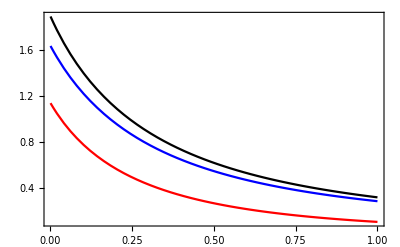
-Graphics-F_1^(d̄-ū)t

```mathematica
F2pn=Labeled[Show[Plot[F2fall[-t],{t,0.001,1},PlotRange->All,PlotStyle->{Black,Thick}],Plot[F2fme[-t],{t,0.001,1},PlotRange->All,PlotStyle->{Red,Thick}],Plot[F2fall[-t]+F2fpo[-t],{t,0.001,1},PlotRange->All,PlotStyle->{Blue,Thick}],AxesStyle->Directive[16],Frame->True,FrameStyle->Directive[Thick,20]],
{SubsuperscriptBox[F,1,OverscriptBox[d,_]-OverscriptBox[u,_]]//DisplayForm,
StyleBox["t",FontSlant->"Italic"]//DisplayForm},{Left,Bottom,Right},LabelStyle->20]
```

```mathematica
path1n=FileNameJoin[{"G:\\calc-online\\gpd\\formfactor\\lowestorder\\result",
"F1udbar-polar.pdf"}];
Export[path1n,F1pn]

path2n=FileNameJoin[{"G:\\calc-online\\gpd\\formfactor\\lowestorder\\result",
"F2udbar-polar.pdf"}];
Export[path2n,F2pn]
```

G:\calc-online\gpd\formfactor\lowestorder\result\F1udbar-polar.pdf

G:\calc-online\gpd\formfactor\lowestorder\result\F2udbar-polar.pdf